```mathematica
Clear["Global`*"]
g={};
Do[
p=1/(1!2^l)(1-s^2)^(m/2)D[((s^2-1)^l), {s,l+m}];
s=Cos[θ];
Y=(-1)^m √(((2l+1)(l-m)!)/(4π (l+m)!))Simplify[p] ⅇ^(ⅈ m ϕ);
r=Abs[Y]^2;
g1=SphericalPlot3D[r,{θ,0,π},{ϕ,0,2 π},Mesh->None,AspectRatio->Automatic,PlotRange->All,Boxed->False,Axes->False,ImageSize->Small,PlotStyle->Directive[Blue,Opacity[0.8],Specularity[White,10]],PlotPoints->100];
AppendTo[g,g1],{l,0,3},{m,0,l}]
```

```mathematica
GraphicsGrid[{{g⟦1⟧},{g⟦2⟧,g⟦3⟧},{g⟦4⟧,g⟦5⟧,g⟦6⟧},{g⟦7⟧,g⟦8⟧,g⟦9⟧,g⟦10⟧}}]
```

-Graphics-

```mathematica
Do[
g[[n]],
{n,1,9}]
```

```mathematica
Clear[n,l,r];
```

```mathematica
a=1;
R[n_,l_,r_]=((2 r)/(n a))^l √((2/(n a))^3((n-l-1)!)/(2 n((n+1)!)))ⅇ^(-r/(n a))LaguerreL[n-l-1,2l+1,2r/(n a)];
```

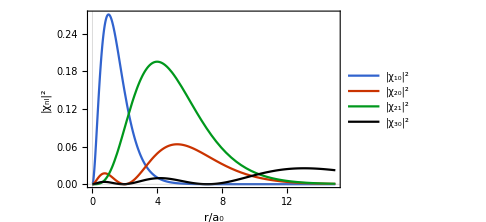

```mathematica
g2=Plot[{(r R[1,0,r])^2,(r R[2,0,r])^2,(r R[2,1,r])^2,(r R[3,0,r])^2},
{r,0,15},PlotRange->All,PlotTheme->"Scientific",
PlotStyle->{Blue,Red,Green,Black},
PlotLegends->Placed[{"|χ_10|^2","|χ_20|^2","|χ_21|^2","|χ_30|^2"},{Right,Center}],
FrameLabel->{"r/a_0","|χ_nl|^2"},
ImageSize->Medium,LabelStyle->{FontFamily->"Times New Roman",FontSize->16,GrayLevel[0]}
]
```

```mathematica
Export["E:\\Document\\Stargazer\\source\\_posts\\氢原子模型\\R.svg",g2]
```

E:\Document\Stargazer\source\_posts\氢原子模型\R.svg